#### Deterministic model with Logistic growth (4 dim when ϵ = 1)

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
(*Some aliases*)
Format[μv]:=Subscript[μ,v];Format[μy]:=Subscript[μ,y];
pars={β,λ,γ,δ,μy, μv,b,K,s,c};
parE={β>0,λ>0,γ>0,δ>0,μy>0, μv>0,b>1,K>0,s>0,c>0};

R0=b β K/(β K+δ);
Clear[K];
(****** Four dim Deterministic  epidemic model with Logistic growth ****)
x1=λ  x(1-(x+y)/K)-   β x v ;
y1=β x v -μy y z- γ y;
v1=-β x v - μv  v z+ b  γ y - δ v;
z1=z(s  y - c z);
ye=c/s; vM=λ(1-ye)/β;
dyn={x1,y1,v1,z1};
dyn3={x1,y1,v1}/.z->0;(*3dim case*)
Print[" (x'
y'
v'
z')=",dyn//FullSimplify//MatrixForm]
Print["b0=",b0=b/.Apart[Solve[R0==1,b][[1]]//FullSimplify]]
(***Fixed point when z->0**)
eq=Thread[dyn3=={0,0,0}];
sol=Solve[eq,{x,y,v}]//FullSimplify;
Es={x,y,v}/.sol[[3]];(*Endemic point with z=0*);
Print["E*=",Est=Es//FullSimplify]
(*Interior equilibria*)
x1s=λ  (1-(x+y)/K)-   β  v ;
z1s=s y - c z;
dyns={x1s,y1,v1,z1s};
el=Eliminate[Thread[dyns=={0,0,0,0}],{x,v,z}];
Qybyelim=Factor[el[[1,1]]-el[[1,2]]]/y//FullSimplify;
Print["Coefficients of  Qy by elim polynomial are:"]
cof=CoefficientList[Qybyelim,y]//FullSimplify
so=y/.Solve[Qybyelim==0,y];(*Third order roots*)
Print["Qybyelim/K,K->Infinity"]
QGuo=Limit[Qybyelim/K,K->Infinity]//Simplify
Print["second order Q of Guo "]
QGuocol=Collect[-QGuo/(c β ((-1+b) c γ-s y μy)),y]
(*****Fixed points of Eric using P(y)***)
fy=(c γ(b-1)-y μy s);
gy=( μv s y+c δ); hy=(γ +y s μy/c);
xe=hy gy/(β fy); ve=y fy/gy; ze= s y /c;
Qy=λ fy gy(1-  y /K)- λ hy gy^2/(β K)-y β fy^2//FullSimplify;
QR=Solve[Qy==0,y];
ym= y/.QR[[1]];
yp=  y/.QR[[2]];yi=  y/.QR[[3]];
```

(x'
y'
v'
z')=(-v x β+x (1-(x+y)/K) λ
v x β-y (γ+z μ_y)
b y γ-v (x β+δ+z μ_v)
z (s y-c z))

b0=1+δ/(K β)

E*={δ/((-1+b) β),(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)),(γ ((-1+b) K β-δ) λ)/(β ((-1+b) K β γ+δ λ))}

Coefficients of  Qy by elim polynomial are:

{c^3 γ δ (K (β-b β)+δ) λ,c^2 ((-1+b) c β γ ((-1+b) K β γ+δ λ)+s λ (γ (K (β-b β)+2 δ) μ_v+δ (K β+δ) μ_y)),c s (s λ μ_v (γ μ_v+K β μ_y+2 δ μ_y)+c β (-δ λ μ_y+(-1+b) γ (λ μ_v-2 K β μ_y))),s^2 μ_y (s λ μ_v^2+c β (-λ μ_v+K β μ_y))}

Qybyelim/K,K->Infinity

c β ((-1+b) c γ-s y μ_y) ((-1+b) c y β γ-c δ λ-s y (λ μ_v+y β μ_y))

second order Q of Guo

c δ λ+y ((1-b) c β γ+s λ μ_v)+s y^2 β μ_y

E*={0.000280348,0.0346317,0.0221859}

E+={0.494238,0.308421,0.00453657,0.308421}

Ei={0.145387,0.284118,0.0131148,0.284118}

E-={0.00228546,0.042969,0.0219482,0.042969}

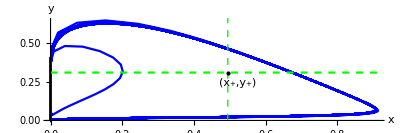

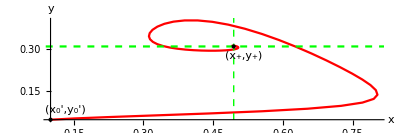

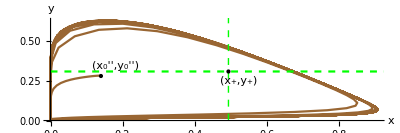

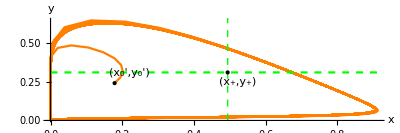

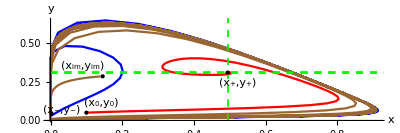

ppG-2LC.pdf

The eigenvalues of E* when b=42 are: {-0.553543+0. ⅈ,0.0166273+0.0823309 ⅈ,0.0166273-0.0823309 ⅈ,0.0346317+0. ⅈ}

The eigenvalues of E+ when b=42 are: {-22.81+0. ⅈ,-0.157506+0.275785 ⅈ,-0.157506-0.275785 ⅈ,-0.301641+0. ⅈ}

The eigenvalues of Ei when b=42 are: {-7.86054+0. ⅈ,-0.116738+0.254012 ⅈ,-0.116738-0.254012 ⅈ,0.264137+0. ⅈ}

The eigenvalues of E- when b=42 are: {-0.842468+0. ⅈ,0.068671+0.167599 ⅈ,0.068671-0.167599 ⅈ,-0.0332964+0. ⅈ}

```mathematica
(************************************ bH < b=42 < b2* *********************************)
(*cn={b->42,μv->1, μy->1,K->1,γ->1/128,β->87/2,λ->1,δ->1/2,s->1, c->1};*)
ClearParameters;tf=2000;
b=42;μv=1; μy=1;K=1;γ=1/128;β=87/2;λ=1;δ=1/2;s=1;c=1;
Print["E*=",Es=Est//N];
Print["E+=",Ep=Chop[{xe,y,ve,ze}/.y->yp//N]]
Print["Ei=",Ei=Chop[{xe,y,ve,ze}/.y->yi//N]]
Print["E-=",Em=Chop[{xe,y,ve,ze}/.y->ym//N]]
X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
(*x0=0.8; y0=0.02;v0=0.01;z0=0.01;*)
x0=0.0022; y0=0.042;v0=0.02;z0=0.04;
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,z[0]==z0};
sol1=NDSolve[ode1,{x,y,v,z},{t,0,tf}];
(*****¨Parametric plot conditions***)
ppb3=ParametricPlot[{  x[t],(y[t])}/.sol1,{t,0,tf}, AxesLabel->{"x","y"},PlotRange->Full,PlotStyle->{Blue},AspectRatio->1/3];
py3=Plot[y/.y->Ep[[2]],{t,0,400},PlotStyle->{Dashed,Green}];
pb3=Show[{ppb3,py3, Graphics[{Green,Dashed,Line[{{x/.x->Ep[[1]],0},{x/.x->Ep[[1]],1}}]}] },Epilog->{{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}}(*,{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-20,10},{x0,y0}]]*)}]
(************************************    Different initial values   **********************************)
x01=0.1; y01=0.05;v01=0.0043;z01=0.1954;
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x01,y[0]==y01,v[0]==v01,z[0]==z01};
sol2=NDSolve[ode1,{x,y,v,z},{t,0,tf}];

ppb3n=ParametricPlot[{  x[t],(y[t])}/.sol2,{t,0,tf}, AxesLabel->{"x","y"},PlotRange->Full,PlotStyle->{Red},AspectRatio->1/3];
py3n=Plot[y/.y->Ep[[2]],{t,0,400},PlotStyle->{Dashed,Green}];
pb3n=Show[{ppb3n,py3n, Graphics[{Green,Dashed,Line[{{x/.x->Ep[[1]],0},{x/.x->Ep[[1]],1}}]}] },Epilog->{{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x01,y01}]},Text["(x_0',y_0')",Offset[{15,10},{x01,y01}]]}]
(************************************    Different initial values   **********************************)
x0i=0.14; y0i=0.28;v0i=0.013;z0i=0.28;
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0i,y[0]==y0i,v[0]==v0i,z[0]==z0i};
soli=NDSolve[ode1,{x,y,v,z},{t,0,tf}];

ppb3n=ParametricPlot[{  x[t],(y[t])}/.soli,{t,0,tf}, AxesLabel->{"x","y"},PlotRange->Full,PlotStyle->{Brown},AspectRatio->1/3];
py3n=Plot[y/.y->Ep[[2]],{t,0,400},PlotStyle->{Dashed,Green}];
pb4=Show[{ppb3n,py3n, Graphics[{Green,Dashed,Line[{{x/.x->Ep[[1]],0},{x/.x->Ep[[1]],1}}]}] },Epilog->{{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x0i,y0i}]},Text["(x_0'',y_0'')",Offset[{15,10},{x0i,y0i}]]}]

(************************************    Different initial values   **********************************)
x0f=Chop[Evaluate[x[t]/.sol1/.t->50//N]][[1]];
y0f=Chop[Evaluate[y[t]/.sol1/.t->50//N]][[1]];
v0f=Chop[Evaluate[v[t]/.sol1/.t->50//N]][[1]];
z0f=Chop[Evaluate[z[t]/.sol1/.t->50//N]][[1]];
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0f,y[0]==y0f,v[0]==v0f,z[0]==z0f};
solf=NDSolve[ode1,{x,y,v,z},{t,0,tf}];

ppb3n=ParametricPlot[{  x[t],(y[t])}/.solf,{t,0,tf}, AxesLabel->{"x","y"},PlotRange->Full,PlotStyle->{Orange},AspectRatio->1/3];
py3n=Plot[y/.y->Ep[[2]],{t,0,400},PlotStyle->{Dashed,Green}];
pbf=Show[{ppb3n,py3n, Graphics[{Green,Dashed,Line[{{x/.x->Ep[[1]],0},{x/.x->Ep[[1]],1}}]}] },Epilog->{{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x0f,y0f}]},Text["(x_0',y_0')",Offset[{15,10},{x0f,y0f}]]}]

epi={{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x01,y01}]},Text["(x_0,y_0)",Offset[{15,10},{x01,y01}]],{PointSize[Large],Style[Point[{Em[[1]],Em[[2]]}],Magenta]},Text["(x_-,y_-)",Offset[{10,4},{Em[[1]],Em[[2]]}]],{PointSize[Large],Style[Point[{Ei[[1]],Ei[[2]]}],Magenta]},Text["(x_im,y_im)",Offset[{-20,10},{Ei[[1]],Ei[[2]]}]](*,{PointSize[Large],Style[Point[{Es[[1]],Es[[2]]}],Magenta]},Text["(x_*,y_*)",Offset[{-20,10},{Es[[1]],Es[[2]]}]]*)};
y11=Show[{pb3,pb3n,pb4},Epilog->epi]
Export["ppG-2LC.pdf",y11]
Jac=Grad[dyn,{x,y,v,z}];
Jacs = Jac//.{x->Es[[1]],y->Es[[2]],v->Es[[3]],z->0}//N;
Print["The eigenvalues of E* when b=42 are: ",Eigenvalues[Jacs]]
Jacp = Jac//.{x->Ep[[1]],y->Ep[[2]],v->Ep[[3]],z->Ep[[4]]}//N;
Print["The eigenvalues of E+ when b=42 are: ",Eigenvalues[Jacp]]
Jaci = Jac//.{x->Ei[[1]],y->Ei[[2]],v->Ei[[3]],z->Ei[[4]]}//N;
Print["The eigenvalues of Ei when b=42 are: ",Eigenvalues[Jaci]]
Jacm = Jac//.{x->Em[[1]],y->Em[[2]],v->Em[[3]],z->Em[[4]]}//N;
Print["The eigenvalues of E- when b=42 are: ",Eigenvalues[Jacm]]
```

E*={0.000280348,0.0346317,0.0221859}

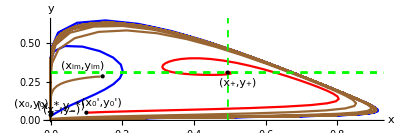

```mathematica
Print["E*=",Es]
epi={{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],
Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x01,y01}]},
Text["(x_0',y_0')",Offset[{15,10},{x01,y01}]],{PointSize[Large],Point[{x0,y0}]},
Text["(x_0,y_0)",Offset[{-20,10},{x0,y0}]],{PointSize[Large],Style[Point[{Em[[1]],Em[[2]]}],Magenta]},
Text["(x_-,y_-)",Offset[{10,4},{Em[[1]],Em[[2]]}]],{PointSize[Large],Style[Point[{Ei[[1]],Ei[[2]]}],Magenta]},
Text["(x_im,y_im)",Offset[{-20,10},{Ei[[1]],Ei[[2]]}]],{PointSize[Large],Style[Point[{Es[[1]],Es[[2]]}],Magenta]},
Text["(x_*,y_*)",Offset[{10,10},{Es[[1]],Es[[2]]}]]};
xy42=Show[{pb3,pb3n,pb4},Epilog->epi]
```

E*={0.000410509,0.0499015,0.0218319}

E+={0.720598,0.213706,0.00151024,0.213706}

Ei={0.0137981-0.00495629 ⅈ,0.108199-0.0179962 ⅈ,0.020184+0.000527643 ⅈ,0.108199-0.0179962 ⅈ}

E-={0.0137981+0.00495629 ⅈ,0.108199+0.0179962 ⅈ,0.020184-0.000527643 ⅈ,0.108199+0.0179962 ⅈ}

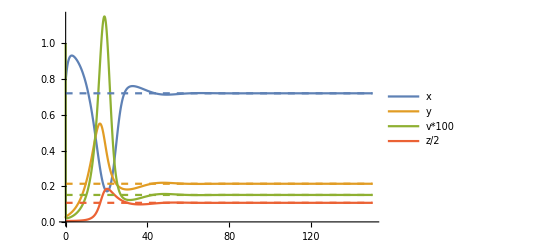

ptH.pdf

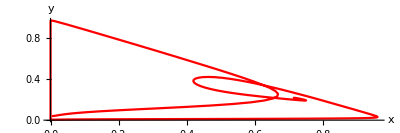

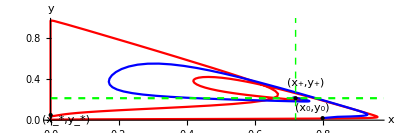

pp29.pdf

The eigenvalues of E* when b=29 are: {-0.567061+0. ⅈ,0.0204906+0.0804108 ⅈ,0.0204906-0.0804108 ⅈ,0.0499015+0. ⅈ}

The eigenvalues of E+ when b=29 are: {-32.3449+0. ⅈ,-0.654873+0. ⅈ,-0.107884+0.185716 ⅈ,-0.107884-0.185716 ⅈ}

The eigenvalues of Ei when b=29 are: {-1.67085+0.294654 ⅈ,0.183885-0.106515 ⅈ,0.0707757+0.115845 ⅈ,-0.0302383-0.0294416 ⅈ}

The eigenvalues of E- when b=29 are: {-1.67085-0.294654 ⅈ,0.183885+0.106515 ⅈ,0.0707757-0.115845 ⅈ,-0.0302383+0.0294416 ⅈ}

```mathematica
(************************************ b=29 < bH  *********************************)
Clear["b"];
b=29;
Print["E*=",Es=Est//N];
Print["E+=",Ep=Chop[{xe,y,ve,ze}/.y->yp//N]]
Print["Ei=",Ei=Chop[{xe,y,ve,ze}/.y->yi//N]]
Print["E-=",Em=Chop[{xe,y,ve,ze}/.y->ym//N]]
X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
x0=0.8; y0=0.02;v0=0.01;z0=0.01;
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,z[0]==z0};
sol1=NDSolve[ode1,{x,y,v,z},{t,0,tf}];
pdy1=Plot[{x[t]/. sol1,y[t]/. sol1,v[t]*100/. sol1,z[t]/2/. sol1},{t,0,150},PlotLegends->{"x","y","v*100","z/2"}];
pEs1=Plot[{x/.x->Ep[[1]],y/.y->Ep[[2]],v*100/.v->Ep[[3]],z/2/.z->Ep[[4]]},{t,0,150},PlotStyle->{Dashed}];
Dyn01=Show[pdy1,pEs1]
Export["ptH.pdf",Dyn01]
(*****¨Parametric plot conditions***)
ppb3=ParametricPlot[{  x[t],(y[t])}/.sol1,{t,0,tf}, AxesLabel->{"x","y"},PlotRange->Full,PlotStyle->{Blue},AspectRatio->1/3];
py3=Plot[y/.y->Ep[[2]],{t,0,400},PlotStyle->{Dashed,Green}];
pb3=Show[{ppb3,py3, Graphics[{Green,Dashed,Line[{{x/.x->Ep[[1]],0},{x/.x->Ep[[1]],1}}]}] },Epilog->{{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-20,10},{x0,y0}]]}];


(************************************    Different initial values   **********************************)
x0i=0.004; y0i=0.04;v0i=0.00001;z0i=0.00001;
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0i,y[0]==y0i,v[0]==v0i,z[0]==z0i};
soli=NDSolve[ode1,{x,y,v,z},{t,0,tf}];

ppb3n=ParametricPlot[{  x[t],(y[t])}/.soli,{t,0,tf}, AxesLabel->{"x","y"},PlotRange->Full,PlotStyle->{Red},AspectRatio->1/3]
epi={{Thick,Text["(x_+,y_+)",Offset[{10,15},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,10},{x0,y0}]],{PointSize[Large],Point[{Es[[1]],Es[[2]]}]},Text["(x_*,y_*)",Offset[{15,-5},{Es[[1]],Es[[2]]}]]};

y11=Show[{ppb3n,pb3},Epilog->epi]
Export["pp29.pdf",y11]
Jac=Grad[dyn,{x,y,v,z}];
Jacs = Jac//.{x->Es[[1]],y->Es[[2]],v->Es[[3]],z->0}//N;
Print["The eigenvalues of E* when b=29 are: ",Eigenvalues[Jacs]]
Jacp = Jac//.{x->Ep[[1]],y->Ep[[2]],v->Ep[[3]],z->Ep[[4]]}//N;
Print["The eigenvalues of E+ when b=29 are: ",Eigenvalues[Jacp]]
Jaci = Jac//.{x->Ei[[1]],y->Ei[[2]],v->Ei[[3]],z->Ei[[4]]}//N;
Print["The eigenvalues of Ei when b=29 are: ",Eigenvalues[Jaci]]
Jacm = Jac//.{x->Em[[1]],y->Em[[2]],v->Em[[3]],z->Em[[4]]}//N;
Print["The eigenvalues of E- when b=29 are: ",Eigenvalues[Jacm]]
```

E*={0.000407598,0.0495653,0.0218397}

E+={0.717945,0.215205,0.00153678,0.215205}

Ei={0.0143072-0.00335392 ⅈ,0.10903-0.0120421 ⅈ,0.0201532+0.000353933 ⅈ,0.10903-0.0120421 ⅈ}

E-={0.0143072+0.00335392 ⅈ,0.10903+0.0120421 ⅈ,0.0201532-0.000353933 ⅈ,0.10903+0.0120421 ⅈ}

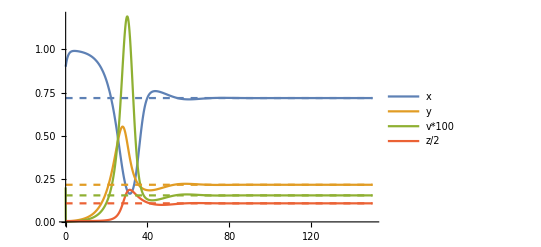

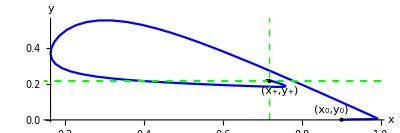

ppH1.pdf

ptH1.pdf

The eigenvalues of E* when b=29.2 are: {-0.566765+0. ⅈ,0.0204074+0.0804544 ⅈ,0.0204074-0.0804544 ⅈ,0.0495653+0. ⅈ}

The eigenvalues of E+ when b=29.2 are: {-32.2336+0. ⅈ,-0.651062+0. ⅈ,-0.108661+0.187036 ⅈ,-0.108661-0.187036 ⅈ}

The eigenvalues of Ei when b=29.2 are: {-1.69485+0.198587 ⅈ,0.168324-0.0905302 ⅈ,0.0750338+0.103646 ⅈ,-0.0200824-0.0263267 ⅈ}

The eigenvalues of E- when b=29.2 are: {-1.69485-0.198587 ⅈ,0.168324+0.0905302 ⅈ,0.0750338-0.103646 ⅈ,-0.0200824+0.0263267 ⅈ}

```mathematica
(************************************ bH < b=29.2 < b1* *********************************)

ClearParameters;tf=1500;
b=29.2;μv=1; μy=1;K=1;γ=1/128;β=87/2;λ=1;δ=1/2;s=1;c=1;
Print["E*=",Es=Est//N];
Print["E+=",Ep=Chop[{xe,y,ve,ze}/.y->yp//N]]
Print["Ei=",Ei=Chop[{xe,y,ve,ze}/.y->yi//N]]
Print["E-=",Em=Chop[{xe,y,ve,ze}/.y->ym//N]]
X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
x0=0.9; y0=0.001;v0=0.002;z0=0.01;
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,z[0]==z0};
sol1=NDSolve[ode1,{x,y,v,z},{t,0,tf}];
pdy1=Plot[{x[t]/. sol1,y[t]/. sol1,v[t]*100/. sol1,z[t]/2/. sol1},{t,0,150},PlotLegends->{"x","y","v*100","z/2"}];
pEs1=Plot[{x/.x->Ep[[1]],y/.y->Ep[[2]],v*100/.v->Ep[[3]],z/2/.z->Ep[[4]]},{t,0,150},PlotStyle->{Dashed}];
Dyn01=Show[pdy1,pEs1]
(*****¨Parametric plot conditions***)
ppb3=ParametricPlot[{  x[t],(y[t])}/.sol1,{t,0,tf}, AxesLabel->{"x","y"},PlotRange->Full,PlotStyle->{Blue},AspectRatio->1/3];
py3=Plot[y/.y->Ep[[2]],{t,0,400},PlotStyle->{Dashed,Green}];
pb3=Show[{ppb3,py3, Graphics[{Green,Dashed,Line[{{x/.x->Ep[[1]],0},{x/.x->Ep[[1]],1}}]}] },Epilog->{{Thick,Text["(x_+,y_+)",Offset[{10,-10},{x/.x->Ep[[1]],y/.y->Ep[[2]]}]],{PointSize[Large],Style[Point[{x/.x->Ep[[1]],y/.y->Ep[[2]]}],Black]}},{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,10},{x0,y0}]]}]
Export["ppH1.pdf",pb3]
Export["ptH1.pdf",Dyn01]
Jac=Grad[dyn,{x,y,v,z}];
Jacs = Jac//.{x->Es[[1]],y->Es[[2]],v->Es[[3]],z->0}//N;
Print["The eigenvalues of E* when b=29.2 are: ",Eigenvalues[Jacs]]
Jacp = Jac//.{x->Ep[[1]],y->Ep[[2]],v->Ep[[3]],z->Ep[[4]]}//N;
Print["The eigenvalues of E+ when b=29.2 are: ",Eigenvalues[Jacp]]
Jaci = Jac//.{x->Ei[[1]],y->Ei[[2]],v->Ei[[3]],z->Ei[[4]]}//N;
Print["The eigenvalues of Ei when b=29.2 are: ",Eigenvalues[Jaci]]
Jacm = Jac//.{x->Em[[1]],y->Em[[2]],v->Em[[3]],z->Em[[4]]}//N;
Print["The eigenvalues of E- when b=29.2 are: ",Eigenvalues[Jacm]]
```

Now, Computations of the Jacobians and Eigenvalues using EcoEvo package:

```mathematica
<<EcoEvo`
(*EcoEvoDocs;*)
ClearParameters;
SetModel[{Pop[x]->{Equation:>dyn[[1]],Color->Red},Pop[y]->{Equation:>dyn[[2]],Color->Green},
Pop[v]->{Equation:> dyn[[3]],Color->Blue},Pop[z]->{Equation:> dyn[[4]],Color->Purple}}]

fpT=SolveEcoEq[]//N
Jp=EcoJacobian[fpT[[6]]]//FullSimplify;
Jim=EcoJacobian[fpT[[7]]]//FullSimplify;
Jm=EcoJacobian[fpT[[8]]]//FullSimplify;
Jst=EcoJacobian[fpT[[4]]]//FullSimplify;
Print["Jac(E_+)=",Jp//MatrixForm]
Print["Jac(E_-)=",Jm//MatrixForm]
Print["Jac(E_im)=",Jim//MatrixForm]
Print["Eigenvalues of E_p are:",eip=EcoEigenvalues[fpT[[6]]]//FullSimplify]
```

EcoEvo Package Version 1.6.4 (November 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

{{x→0.,y→0.,v→0.,z→0.},{x→1.,y→0.,v→0.,z→0.},{x→1.,y→0.,v→0.,z→0.},{x→0.000280348,y→0.0346317,v→0.0221859,z→0.},{x→0.,y→-0.0078125,v→-0.00520833,z→-0.0078125},{x→0.494238,y→0.308421,v→0.00453657,z→0.308421},{x→0.145387,y→0.284118,v→0.0131148,z→0.284118},{x→0.00228546,y→0.042969,v→0.0219482,z→0.042969}}

Jac(E_+)=(-0.494238 | -0.494238 | -21.4993 | 0
0.197341 | -0.316234 | 21.4993 | -0.308421
-0.197341 | 21/64 | -22.3078 | -0.00453657
0 | 0.308421 | 0 | -0.308421)

Jac(E_-)=(-0.00228546 | -0.00228546 | -0.0994175 | 0
0.954746 | -0.0507815 | 0.0994175 | -0.042969
-0.954746 | 21/64 | -0.642387 | -0.0219482
0 | 0.042969 | 0 | -0.042969)

Jac(E_im)=(-0.145387 | -0.145387 | -6.32433 | 0
0.570495 | -0.29193 | 6.32433 | -0.284118
-0.570495 | 21/64 | -7.10845 | -0.0131148
0 | 0.284118 | 0 | -0.284118)

Eigenvalues of E_p are:{-22.81,-0.157506+0.275785 ⅈ,-0.157506-0.275785 ⅈ,-0.301641}

{x→0.0022,y→0.042}

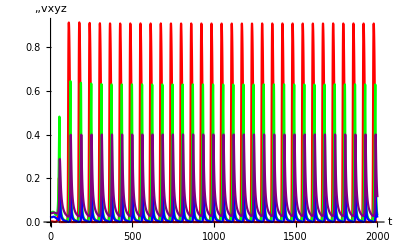

The floquet exponents are

{0.314283,0.0000123842,-0.999987,-44.3216}

soltF.pdf

```mathematica
(*Time plot corresponding to the blue curve**)
fpT[[6]];
Epn=RuleListTweak[{x->x0,y->y0},{y},{0}]
sol=EcoSim[Epn,1500];
pt=PlotDynamics[sol1,PlotPoints->200]
lc=FindEcoCycle[FinalSlice[{sol1[[1,1]],sol1[[1,2]]}]];
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["soltF.pdf",pt]
```

{x→0.1,y→0.05}

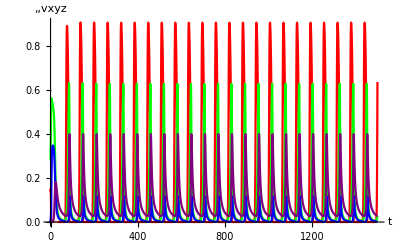

The floquet exponents are

{0.314283,0.0000108179,-0.999989,-44.3216}

soltB.pdf

```mathematica
(*Time plot corresponding to the brown curve**)
Epn=RuleListTweak[{x->x01,y->y01},{y},{0}]
sol=EcoSim[Epn,tf];
pt=PlotDynamics[soli,PlotPoints->200]
lc=FindEcoCycle[FinalSlice[{soli[[1,1]],soli[[1,2]]}]];
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["soltB.pdf",pt]
```

```mathematica
X0={x0,y0,v0};
X01={x01,y01,v01};
X0i={x0i,y0i,v0i};
X0f={x0f,y0f,v0f};

Ep3={x,y,v}//.Drop[fpT[[6]],-1]
Epi={x,y,v}//.Drop[fpT[[7]],-1]
pp3D=ParametricPlot3D[{{  x[t],y[t],v[t]}/.sol1,{  x[t],y[t],v[t]}/.sol2,{  x[t],y[t],v[t]}/.soli,
{  x[t],y[t],v[t]}/.solf},{t,0,tf}, 
BoxRatios->{1,1,1},AxesLabel->{"x","y","v"},PlotPoints->200, PlotRange->Full,PlotStyle->{Blue, Red,Brown,Orange}];
pt0={PointSize@.02, Style[Point[X0],Black]};pt0s=Text[Style["(x_-,y_-,v_-)", 10], X0];
pt01={PointSize@.02, Style[Point[X01],Black]};pt01s=Text[Style["(x_0,y_0,v_0)", 10], X01];
pt0i={PointSize@.02, Style[Point[Epi],Black]};pt0is=Text[Style["(x_im,y_im,v_im)", 10], Epi];
pts={PointSize@.02, Style[Point[Ep3],Black]}; ptss=Text[Style["(x_+,y_+,v_+)", 10] ,Ep3 
];
ptf={PointSize@.02, Style[Point[X0f],Black]}; ptfs=Text[Style["(x_0',y_0',v_0')", 10] ,X0f];
pts={ptss,pt0,pt0s,pts,pt01,pt01s,pt0i,pt0is,ptf,ptfs};
cy3=Show[{pp3D}, Graphics3D[pts], Axes -> True,
 BoxRatios -> 1]
 (*Export["cy3D.pdf",cy3]*)
```

{0.494238,0.308421,0.00453657}

{0.145387,0.284118,0.0131148}

-Graphics3D-

```mathematica
X0={x0,y0,z0};
X01={x01,y01,z01};
X0i={x0i,y0i,z0i};
Ep3={x,y,z}//.Drop[fpT[[6]],{3}]
Epi={x,y,z}//.Drop[fpT[[7]],{3}]
pp3D=ParametricPlot3D[{{  x[t],y[t],z[t]}/.sol1,{  x[t],y[t],z[t]}/.sol2,{  x[t],y[t],z[t]}/.soli},{t,0,tf}, 
BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotPoints->200, PlotRange->Full,PlotStyle->{Blue, Red,Brown}];
pt0={PointSize@.02, Style[Point[X0],Black]};pt0s=Text[Style["(x_-,y_-,z_-)", 10], X0];
pt01={PointSize@.02, Style[Point[X01],Black]};pt01s=Text[Style["(x_0,y_0,z_0)", 10], X01];
pt0i={PointSize@.02, Style[Point[Epi],Black]};pt0is=Text[Style["(x_im,y_im,z_im)", 10], Epi];
pts={PointSize@.02, Style[Point[Ep3],Black]}; ptss=Text[Style["(x_+,y_+,z_+)", 10] ,Ep3 ];
pts={ptss,pt0,pt0s,pts,pt01,pt01s,pt0i,pt0is};
cy3=Show[{pp3D}, Graphics3D[pts], Axes -> True,
 BoxRatios -> 1]
 Export["cy3Dz.pdf",cy3]
```

{0.494238,0.308421,0.308421}

{0.145387,0.284118,0.284118}

-Graphics3D-

cy3Dz.pdf